# Lucretius Update

Marcos  Costa  Santos  Carreira

## Distributions

```mathematica
shadowmomp[dist_,K_,p_]:=Integrate[x^p*PDF[dist,x],{x,K,+∞},Assumptions->K>0&&p>=0&&p∈Integers];
```

```mathematica
distinfo[dist_]:=Append[Transpose[{{"PDF","CDF","SF"},
Comap[{PDF[#,x]&,CDF[#,x]&,SurvivalFunction[#,x]&},dist]}],
{"ICDF",FullSimplify[Refine[InverseCDF[dist,p],0<p<1]]}];
```

## Uniform

```mathematica
Grid[distinfo[UniformDistribution[{0,1}]],Frame->All]
```

PDF | Piecewise[{{1, 0≤x≤1}, {0, True}}]
CDF | Piecewise[{{x, 0≤x≤1}, {1, x>1}, {0, True}}]
SF | Piecewise[{{1-x, 0≤x≤1}, {0, x>1}, {1, True}}]
ICDF | p

```mathematica
shadowmomp[UniformDistribution[{0,1}],K,p]
```

Piecewise[{{-(-1+K^(1+p))/(1+p), 0<K<1}, {0, True}}]

## Gaussian

```mathematica
Grid[distinfo[NormalDistribution[μ,σ]],Frame->All]
```

PDF | (ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)
CDF | 1/2 Erfc[(-x+μ)/(√2 σ)]
SF | 1/2 Erfc[(x-μ)/(√2 σ)]
ICDF | μ-√2 σ InverseErfc[2 p]

```mathematica
shadowmomp[NormalDistribution[μ,σ],K,p]
```

Integrate[(ⅇ^(-(x-μ)^2/(2 σ^2)) x^p)/(√(2 π) σ),{x,K,∞},Assumptions→K>0&&p≥0&&p∈ℤ]

```mathematica
shadowmomp[NormalDistribution[0,1],K,p]
```

(2^(-1+p/2) Gamma[(1+p)/2,K^2/2])/(√π)

## Cauchy

```mathematica
Grid[distinfo[CauchyDistribution[μ,γ]],Frame->All]
```

PDF | 1/(π γ (1+(x-μ)^2/γ^2))
CDF | 1/2+ArcTan[(x-μ)/γ]/π
SF | 1/2-ArcTan[(x-μ)/γ]/π
ICDF | μ-γ Cot[p π]

```mathematica
shadowmomp[CauchyDistribution[0,1],K,p]
```

ConditionalExpression[(K^(-1+p) Hypergeometric2F1[1,(1-p)/2,(3-p)/2,-1/K^2])/(π-p π), p<1]

```mathematica
Refine[shadowmomp[CauchyDistribution[0,γ],K,0],γ>0&&K>0]
```

ArcTan[γ/K]/π

## Student’s T

```mathematica
Grid[distinfo[StudentTDistribution[μ,σ,ν]],Frame->All]
```

PDF | ((ν/(ν+(x-μ)^2/σ^2))^((1+ν)/2))/(√ν σ Beta[ν/2,1/2])
CDF | Piecewise[{{1/2 BetaRegularized[(ν σ^2)/((x-μ)^2+ν σ^2),ν/2,1/2], x≤μ}, {1/2 (1+BetaRegularized[(x-μ)^2/((x-μ)^2+ν σ^2),1/2,ν/2]), True}}]
SF | Piecewise[{{1/2 BetaRegularized[(ν σ^2)/((-x+μ)^2+ν σ^2),ν/2,1/2], -x≤-μ}, {1/2 (1+BetaRegularized[(-x+μ)^2/((-x+μ)^2+ν σ^2),1/2,ν/2]), True}}]
ICDF | Piecewise[{{μ-√ν σ √(-1+1/InverseBetaRegularized[2 p,ν/2,1/2]), 2 p<1}, {μ, 2 p==1}, {μ+√ν σ √(-1+1/InverseBetaRegularized[2-2 p,ν/2,1/2]), True}}]

```mathematica
xab==1-1-xba
```

```mathematica
1/2 ((x-μ)^2/((x-μ)^2+ν σ^2)1/2ν/2+1)->1/2 (1-(ν σ^2)/((x-μ)^2+ν σ^2)ν/21/2+1)->1-1/2 ((ν σ^2)/((x-μ)^2+ν σ^2)ν/21/2)
```

```mathematica
Refine[InverseBetaRegularized[1,ν/2,1/2],ν>1]
```

1

```mathematica
Refine[shadowmomp[StudentTDistribution[0,1,ν],K,p],ν>0&&p<ν]
```

(K^(p-ν) ν^(-1/2+(1+ν)/2) Hypergeometric2F1[(1+ν)/2,1/2 (-p+ν),1/2 (2-p+ν),-ν/K^2])/((-p+ν) Beta[ν/2,1/2])

## Pareto

```mathematica
Grid[distinfo[ParetoDistribution[L,α]],Frame->All]
```

PDF | Piecewise[{{L^α x^(-1-α) α, x≥L}, {0, True}}]
CDF | Piecewise[{{1-(L/x)^α, x≥L}, {0, True}}]
SF | Piecewise[{{(x/L)^-α, x≥L}, {1, True}}]
ICDF | L (1-p)^(-1/α)

```mathematica
Refine[shadowmomp[ParetoDistribution[L,α],K,p],K>L>0&&α>p>0]
```

-(K^(p-α) L^α α)/(p-α)

## Truncated Pareto

```mathematica
tpPDF[L_,H_,α_,x_]:=(α*L^α*x^(-α-1))/(1-(L/H)^α);
```

```mathematica
tp=ProbabilityDistribution[(α*L^α*x^(-α-1))/(1-(L/H)^α),{x,L,H}]
```

ProbabilityDistribution[(x^(-1-α) L^α α)/(1-(L/H)^α),{x,L,H}]

```mathematica
Grid[Refine[distinfo[tp],0<L<x<H],Frame->All]
```

PDF | (L^α x^(-1-α) α)/(1-(L/H)^α)
CDF | -(x^-α (-L^α+x^α))/(-1+(L/H)^α)
SF | 1+(x^-α (-L^α+x^α))/(-1+(L/H)^α)
ICDF | (L^-α (1+(-1+(L/H)^α) p))^(-1/α)

```mathematica
FullSimplify[PowerExpand[(L^-α (1+(-1+(L/H)^α) p))^(-1/α)]]
```

L (1+(-1+H^-α L^α) p)^(-1/α)

```mathematica
tpSF[L_,H_,α_,x_]:=1+(x^-α (-L^α+x^α))/(-1+(L/H)^α);
```

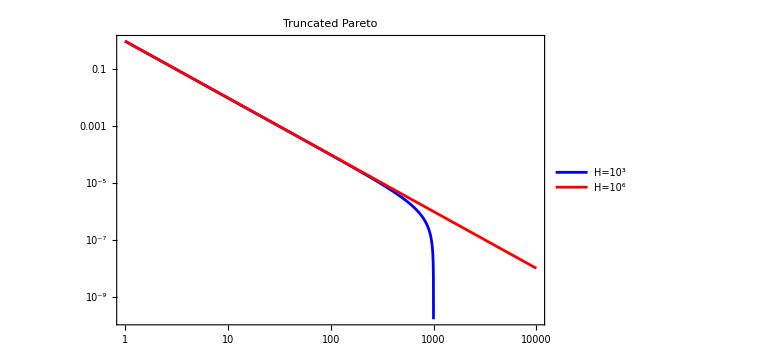

```mathematica
LogLogPlot[{
tpSF[1,10^3,2,x],
tpSF[1,10^6,2,x]},{x,1,10^4},
ImageSize->Large,PlotRange->All,Frame->True,
PlotStyle->{Blue,Red},
PlotLegends->{"H=10^3","H=10^6"},
PlotLabel->"Truncated Pareto"]
```

```mathematica
tpICDF[L_,H_,α_,p_]:=L (1-(1- (L/H)^α) p)^(-1/α);
```

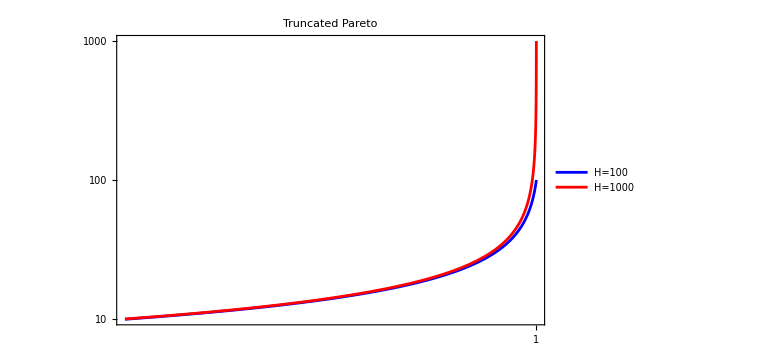

```mathematica
LogLogPlot[{
tpICDF[1,100,2,p],
tpICDF[1,1000,2,p]},{p,0.99,1},
ImageSize->Large,PlotRange->All,Frame->True,
PlotStyle->{Blue,Red},
PlotLegends->{"H=100","H=1000"},
PlotLabel->"Truncated Pareto"]
```

```mathematica
FullSimplify[PowerExpand[Refine[shadowmomp[tp,K,p],H>K>L>0&&α>p>0]]]
```

(K^-α (H^α K^p-H^p K^α) L^α α)/((H^α-L^α) (-p+α))

```mathematica
(( K^(p-α)-H^(p-α) ) L^α α)/((1-(L/H)^α) (α-p))
```

```mathematica
FullSimplify[PowerExpand[Mean[tp]]]
```

((H^α L-H L^α) α)/((H^α-L^α) (-1+α))

```mathematica
FullSimplify[PowerExpand[(K^-α (H^α K^p-H^p K^α) L^α α)/((H^α-L^α) (-p+α))/.p->1]]
```

(K^-α (H^α K-H K^α) L^α α)/((H^α-L^α) (-1+α))

## LogNormal

```mathematica
Grid[distinfo[LogNormalDistribution[μ,σ]],Frame->All]
```

PDF | Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]
CDF | Piecewise[{{1/2 Erfc[(μ-Log[x])/(√2 σ)], x>0}, {0, True}}]
SF | Piecewise[{{1/2 Erfc[-(μ-Log[x])/(√2 √(σ^2))], x>0}, {0, True}}]
ICDF | ⅇ^(μ-√2 σ InverseErfc[2 p])

```mathematica
shadowmomp[LogNormalDistribution[0,1],K,p]
```

1/2 ⅇ^(p^2/2) (1+Erf[(p-Log[K])/(√2)])

## Power Law

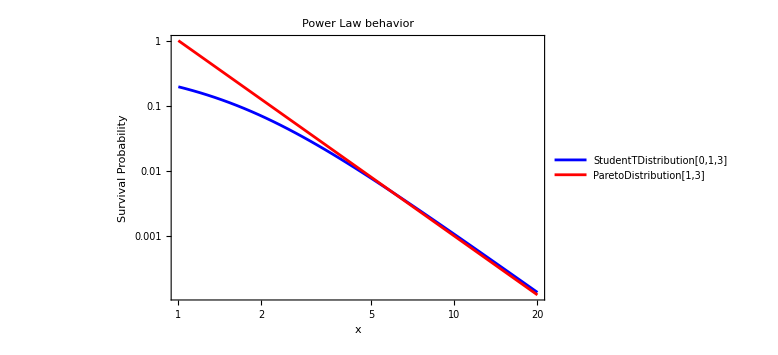

```mathematica
LogLogPlot[{SurvivalFunction[StudentTDistribution[0,1,3],x],
SurvivalFunction[ParetoDistribution[1,3],x]},{x,1,20},
Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->{Blue,Red},
AxesOrigin->{5,SurvivalFunction[StudentTDistribution[0,1,3],5]},PlotLabel->"Power Law behavior",
PlotLegends->{"StudentTDistribution[0,1,3]","ParetoDistribution[1,3]"},
FrameLabel->{"x","Survival Probability"}]
```

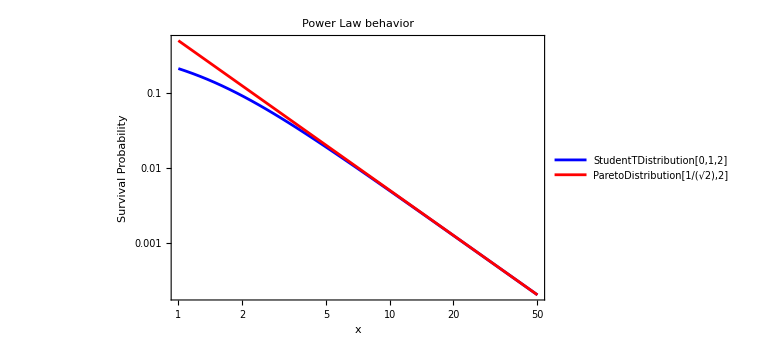

```mathematica
LogLogPlot[{SurvivalFunction[StudentTDistribution[0,1,2],x],
SurvivalFunction[ParetoDistribution[1/(√2),2],x]},{x,1,50},
Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->{Blue,Red},
AxesOrigin->{7,SurvivalFunction[StudentTDistribution[0,1,2],7]},PlotLabel->"Power Law behavior",
PlotLegends->{"StudentTDistribution[0,1,2]","ParetoDistribution[1/(√2),2]"},
FrameLabel->{"x","Survival Probability"}]
```

## Records

### Pareto and Frechet

```mathematica
ψ[L_,α_,n_,x_]:=n(1-(L/x)^α)^(n-1)(L/x)^α  (α/x);
```

```mathematica
φ[α_,β_,x_]:=(α/x)(β/x)^α Exp[-(β/x)^α];
```

```mathematica
PowerExpand[ψ[L,α,n,x]/φ[α,β,x]]
```

ⅇ^(x^-α β^α) L^α n (1-L^α x^-α)^(-1+n) β^-α

```mathematica
ⅇ^((x/β)^-α) (L/β)^α n (1-L^α x^-α)^(-1+n)
```

ⅇ^((x/β)^-α) n (1-L^α x^-α)^(-1+n) (L/β)^α

```mathematica
Limit[ⅇ^((x/β)^-α) n (1-L^α x^-α)^(-1+n) (L/β)^α,x->∞]
```

ConditionalExpression[n (L/β)^α, ((1/β)^-α|n|L^α|(L/β)^α)∈ℝ&&α>0]

```mathematica
hmomFre[L_,α_,n_,y_,p_]:=n L^(-(α p)/(α-p))(y(1-p/α))^(p/(α-p))Exp[-n L^(-(α p)/(α-p))(y(1-p/α))^(α/(α-p)) ];
```

```mathematica
hmomFrez[λ_,α_,z_,p_]:=λ(z)^(p/(α-p))Exp[-λ(z)^(α/(α-p)) ];
```

Divide by (1-p/α) (going from dy to dz)

```mathematica
Integrate[(λ(z)^(p/(α-p))Exp[-λ(z)^(α/(α-p)) ])/(1-p/α),z,
Assumptions->λ>0&&0<p<α&&α>1]
```

-ⅇ^(-z^(α/(-p+α)) λ)

```mathematica
Integrate[(λ(z)^(p/(α-p))Exp[-λ(z)^(α/(α-p))])/(1-p/α),{z,0,+∞},
Assumptions->λ>0&&0<p<α&&α>1]
```

1

```mathematica
hmomFrezdist=ProbabilityDistribution[(λ(z)^(p/(α-p)))/(1-p/α)Exp[-λ(z)^(α/(α-p)) ],{z,0,+∞},
Assumptions->λ>0&&0<p<α&&α>1]
```

ProbabilityDistribution[(x^(p/(-p+α)) ⅇ^(-x^(α/(-p+α)) λ) λ)/(1-p/α),{x,0,∞},Assumptions→λ>0&&0<p<α&&α>1]

```mathematica
Mean[hmomFrezdist]
```

λ^(-1+p/α) Gamma[2-p/α]

### Uniform

H=x^n

h=n*x^(n-1)

```mathematica
Mean[ProbabilityDistribution[n x^(n-1),{x,0,1},Assumptions->n>=2&&n∈Integers]]
```

n/(1+n)

```mathematica
meanunifpts=Chop[N[Table[{n,n/(1+n),n (n/(1+n))^(n-1)},
{n,1,20}]]];
```

```mathematica
Show[DiscretePlot3D[n x^(n-1),{n,1,20},{x,0,1,0.01},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Uniform - Record Distribution and Mean"],
ListLinePlot3D[meanunifpts,PlotStyle->{Thick,Black}]]
```

-Graphics3D-

```mathematica
Timing[dtsunif=Table[Most[tmax[RandomVariate[UniformDistribution[{0,1}],10000]]],{100000}];]
```

{292.708,Null}

```mathematica
Show[Histogram3D[Log[1-Flatten[dtsunif,1]],Automatic,"PDF",ImageSize->Large,
AxesLabel->{"Log[1-K]","Log[1/δt]"},ChartElementFunction->"GradientScaleCube",
PlotLabel->"Uniform - Record Persistence"],
ListLinePlot3D[{{0,0,0.05},{-10,-10,0.05}}]]
```

-Graphics3D-

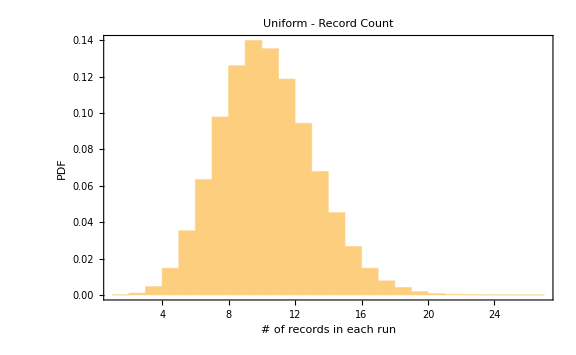

```mathematica
Histogram[Map[Length,dtsunif]+1,Automatic,"PDF",Frame->True,PlotRange->All,
AxesOrigin->{Log[10000]+EulerGamma,0},ImageSize->Large,
FrameLabel->{"# of records in each run","PDF"},
PlotLabel->"Uniform - Record Count"]
```

```mathematica
{Mean[Map[Length,dtsunif]]+1.,Log[10000.]+EulerGamma}
```

{9.78565,9.78756}

### Pareto

H=(1-(L/x)^α)^n

h=n*(1-(L/x)^α)^(n-1)(α/x)(L/x)^α

```mathematica
parint=IntegrateChangeVariables[Inactive[Integrate][α n (1-(L/x)^α)^(-1+n) (L/x)^α,{x,L,+∞},
Assumptions->n>=2&&α>1&&L>0],u,u==(L/x)^α]
```

IntegrateChangeVariables[Integrate[n (1-(L/x)^α)^(-1+n) (L/x)^α α,{x,L,∞},Assumptions→n≥2&&α>1&&L>0],u,u==(L/x)^α]

```mathematica
Timing[Activate[parint]]
```

{14.4937,IntegrateChangeVariables[-(L π Csc[n π] Gamma[(-1+α)/α])/(Gamma[-n] Gamma[1+n-1/α]),u,u==(L/x)^α]}

```mathematica
FullSimplify[Gamma[n]Gamma[1-n]]
```

π Csc[n π]

```mathematica
Gamma[1+n-1/α]==(n-1/α) Gamma[n-1/α]
```

```mathematica
Gamma[1-n]==(-n) Gamma[-n]
```

```mathematica
Gamma[1-1/α]==(-1/α) Gamma[-1/α]
```

```mathematica
-(L π Csc[n π] Gamma[(-1+α)/α])/(Gamma[-n] Gamma[1+n-1/α])->-(L Gamma[n]Gamma[1-n] Gamma[1-1/α])/(Gamma[-n] (n-1/α) Gamma[n-1/α])->-(L Gamma[n](-n) Gamma[-n] (-1/α) Gamma[-1/α])/(Gamma[-n] (n-1/α) Gamma[n-1/α])->
```

```mathematica
-(L n Gamma[n]Gamma[-1/α])/(α  (n-1/α) Gamma[n-1/α])->-(L n Beta[n,-1/α])/(α  (n-1/α))
```

```mathematica
Integrate[L*(1-p)^(-1/α)*n*p^(n-1),{p,0,1},Assumptions->n>=2&&α>1&&L>0]
```

(L n Gamma[n] Gamma[(-1+α)/α])/Gamma[1+n-1/α]

```mathematica
(L n Gamma[n] Gamma[(-1+α)/α])/Gamma[1+n-1/α]->(L n Gamma[n] (-1/α) Gamma[-1/α])/((n-1/α) Gamma[n-1/α])->-(L n Gamma[n]  Gamma[-1/α])/(α  (n-1/α) Gamma[n-1/α])
```

```mathematica
paretoKdist[L_,α_,n_,x_]:=n*(1-(L/x)^α)^(n-1)*(α/x)*(L/x)^α;
```

```mathematica
meanparetof[L_,α_,n_]:=-(L n Beta[n,-1/α])/(α  (n-1/α));
```

```mathematica
meanpareto3pts=Chop[N[Table[{n,meanparetof[1,3,n],paretoKdist[1,3,n,meanparetof[1,3,n]]},
{n,50,1000,50}]]];
```

```mathematica
Show[DiscretePlot3D[paretoKdist[1,3,n,x],{n,10,1000,10},{x,1,20,0.1},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Pareto - Record Distribution and Mean",
Filling->None],
ListLinePlot3D[meanpareto3pts,PlotStyle->{Thick,Black}]]
```

-Graphics3D-

```mathematica
paretoω0[n_,x_]:=n*(1-x)^(n-1);
```

```mathematica
Plot3D[paretoω0[n,x],{n,1,20},{x,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Mean[ProbabilityDistribution[n*(1-x)^(n-1),{x,0,1}]]
```

1/(1+n)

```mathematica
meanpareto3shp0pts=Chop[N[Table[{n,1/(1+n),paretoω0[n,1/(1+n)]},
{n,2,50}]]];
```

```mathematica
Show[DiscretePlot3D[paretoω0[n,x],{n,2,50},{x,0,1,0.001},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Pareto - Shadow Moment p=0 Distribution and Mean",
Filling->None],
ListLinePlot3D[meanpareto3shp0pts,PlotStyle->{Thick,Black}]]
```

-Graphics3D-

```mathematica
Mean[ProbabilityDistribution[n*(x*L^-α*(1-0/α))^(0/(α-1))*(1-(x*L^-0*(1-0/α))^(α/(α-0)))^(n-1),
{x,0,1},Assumptions->n>=2&&α>1&&L>0]]
```

1/(1+n)

```mathematica
paretoω1[L_,α_,n_,x_]:=n*(x*L^-α*(1-1/α))^(1/(α-1))*(1-(x*L^-1*(1-1/α))^(α/(α-1)))^(n-1);
```

```mathematica
paretoω1[1,α,2,x]
```

2 (1-(x (1-1/α))^(α/(-1+α))) (x (1-1/α))^(1/(-1+α))

```mathematica
FullSimplify[Solve[1-L^(-(α*p)/(α-p))*(x*(1-p/α))^(α/(α-p))==0,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-((L^((p α)/(-p+α)))^(1-p/α) α)/(p-α)}}

```mathematica
α/(α-p)(L^((p α)/(α-p)))^(1-p/α)
```

```mathematica
Plot3D[paretoω1[1,2,n,x],{n,2,20},{x,0,2}]
```

-Graphics3D-

```mathematica
Plot3D[paretoω1[1,3,n,x],{n,2,20},{x,0,2}]
```

-Graphics3D-

```mathematica
Plot3D[paretoω1[1,4,n,x],{n,2,20},{x,0,2}]
```

-Graphics3D-

```mathematica
Simplify[Integrate[n*(x*(1-1/α))^(1/(α-1))*(1-(x*(1-1/α))^(α/(α-1)))^(n-1),
{x,0,α/(α-1)},Assumptions->n>=2&&α>1]]
```

1

```mathematica
Simplify[Mean[ProbabilityDistribution[n*(x*(1-1/α))^(1/(α-1))*(1-(x*(1-1/α))^(α/(α-1)))^(n-1),
{x,0,α/(α-1)},Assumptions->n>=2&&α>1]]]
```

(n π ((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α)) Csc[n π] Gamma[2-1/α])/(Gamma[1-n] Gamma[2+n-1/α])

```mathematica
(n π ((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α)) Csc[n π] Gamma[2-1/α])/(Gamma[1-n] Gamma[2+n-1/α])->(n  (1-1/α)^(1/(-1+α))(1-1/α)^(-α/(-1+α)) Gamma[n]Gamma[1-n] Gamma[2-1/α])/(Gamma[1-n] Gamma[2+n-1/α])->
```

```mathematica
(n  (1-1/α)^((1-α)/(-1+α)) Gamma[n]Gamma[2-1/α])/Gamma[2+n-1/α]->(n  Beta[n,2-1/α])/(1-1/α)
```

```mathematica
meanpareto3shp1[α_,n_]:=(n  Beta[n,2-1/α])/(1-1/α);
```

```mathematica
meanpareto3shp1pts=Chop[N[Table[{n,meanpareto3shp1[3,n],paretoω1[1,3,n,1/(1+n)]},
{n,2,50}]]];
```

```mathematica
Show[DiscretePlot3D[paretoω1[1,3,n,x],{n,2,50},{x,0,3/2,0.001},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Pareto - Shadow Moment p=1 Distribution and Mean",
Filling->None],
ListLinePlot3D[meanpareto3shp1pts,PlotStyle->{Thick,Black}]]
```

-Graphics3D-

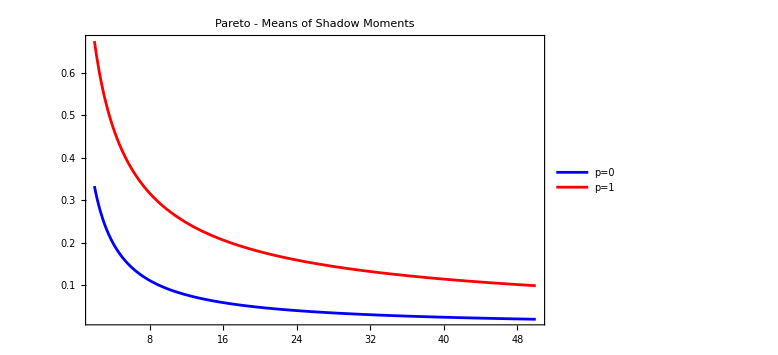

```mathematica
Plot[{1/(n+1),meanpareto3shp1[3,n]},{n,2,50},Frame->True,
PlotRange->All,PlotLegends->{"p=0","p=1"},ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Pareto - Means of Shadow Moments"]
```

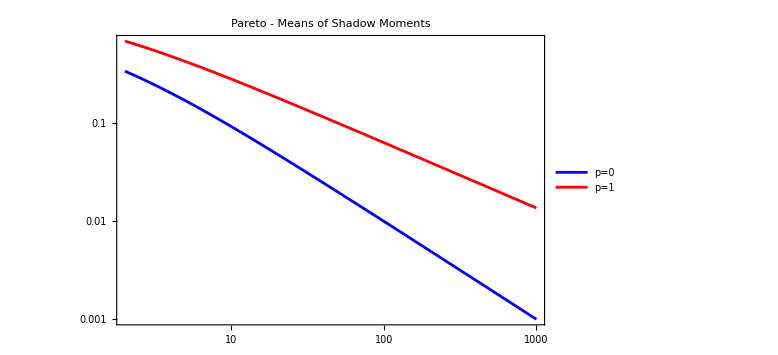

```mathematica
LogLogPlot[{1/(n+1),meanpareto3shp1[3,n]},{n,2,1000},Frame->True,
PlotRange->All,PlotLegends->{"p=0","p=1"},ImageSize->Large,
PlotStyle->{Blue,Red},PlotLabel->"Pareto - Means of Shadow Moments"]
```

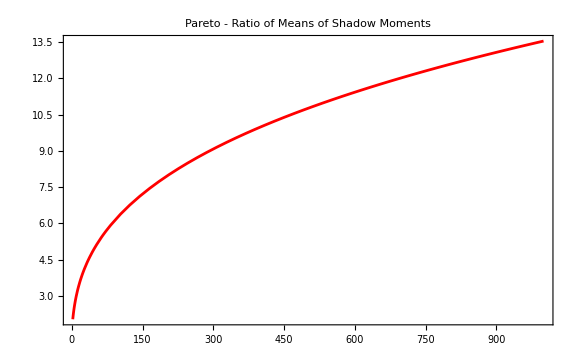

```mathematica
Plot[(n+1)meanpareto3shp1[3,n],{n,2,1000},Frame->True,
PlotRange->All,ImageSize->Large,
PlotStyle->{Red},PlotLabel->"Pareto - Ratio of Means of Shadow Moments"]
```

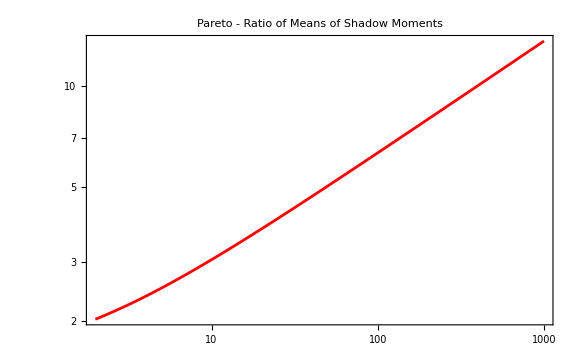

```mathematica
LogLogPlot[(n+1)meanpareto3shp1[3,n],{n,2,1000},Frame->True,
PlotRange->All,ImageSize->Large,
PlotStyle->{Red},PlotLabel->"Pareto - Ratio of Means of Shadow Moments"]
```

```mathematica
paretoKdistc0[L_,α_,n_,x_]:=n*(1-(L/x)^α)^(n-1)*(α/x)*(α/(α-1))*(L/x)^α;
```

```mathematica
meanpareto3shp1c0pts=Chop[N[Table[{n,(n+1)meanpareto3shp1[3,n],paretoKdistc0[1,3,n,(n+1)meanpareto3shp1[3,n]]},
{n,2,1002,50}]]];
```

```mathematica
Show[DiscretePlot3D[paretoKdistc0[1,3,n,x],{n,2,1002,50},{x,1,20,0.01},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Pareto - Conditional Shadow Moment p=1 Distribution and Mean",
Filling->None],
ListLinePlot3D[meanpareto3shp1c0pts,PlotStyle->{Thick,Black}]]
```

-Graphics3D-

### Truncated Pareto

```mathematica
((1-(L/x)^α)/(1-(L/H)^α))^n
```

```mathematica
FullSimplify[D[((1-(L/x)^α)/(1-(L/H)^α))^n,x]]
```

(n ((-1+(L/x)^α)/(-1+(L/H)^α))^n (L/x)^α α)/(x-(L/x)^α x)

```mathematica
FullSimplify[Solve[Y==((1-(L/X)^α)/(1-(L/H)^α))^n,X]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{X→L (1+(-1+(L/H)^α) Y^(1/n))^(-1/α)}}

```mathematica
(1-(L/H)^α)->η
```

```mathematica
L (1-(1-(L/H)^α) Y^(1/n))^(-1/α)/.(1-(L/H)^α)->η
```

L (1-Y^(1/n) η)^(-1/α)

```mathematica
(( K^(p-α)-H^(p-α) ) L^α α)/(η (α-p))
```

```mathematica
Expand[PowerExpand[(( (L (1-Y^(1/n) η)^(-1/α))^(p-α)-H^(p-α) )L^α α)/(η (α-p))]]
```

-(H^(p-α) L^α α)/((-p+α) η)+(L^p α (1-Y^(1/n) η)^(-(p-α)/α))/((-p+α) η)

```mathematica
Expand[PowerExpand[(( (L (1-Y^(1/n) η)^(-1/α))^(p-α)-H^(p-α) )L^α α)/(η (α-p))]]==Expand[PowerExpand[(α L^p((1-η Y^(1/n))^(-(p-α)/α)-(L/H)^(-(p-α))))/(η(α-p))]]
```

True

```mathematica
FullSimplify[Solve[x==-(H^(p-α) L^α α)/((-p+α) η)+(L^p α (1-Y^(1/n) η)^(-(p-α)/α))/((-p+α) η),Y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Y→((1-(L^-p (H^(p-α) L^α+(x (-p+α) η)/α))^(-α/(p-α)))/η)^n}}

```mathematica
((1-((L/H)^(-(p-α))+x η L^-p (1-p/α))^(α/(α-p)))/η)^n
```

```mathematica
g[L_,H_,α_,p_,x_]:=Module[{η},
η=(1-(L/H)^α);
x*η*L^-p*(1-p/α)+(L/H)^(α-p)];
```

```mathematica
swtpSF[L_,H_,α_,p_,n_,x_]:=Module[{η},
η=(1-(L/H)^α);
((1-(g[L,H,α,p,x])^(α/(α-p)))/η)^n];
```

```mathematica
FullSimplify[D[1-((1-(gg[x])^(α/(α-p)))/η)^n,x]]
```

(n α gg[x]^(p/(-p+α)) (-(-1+gg[x]^(α/(-p+α)))/η)^(-1+n) gg'[x])/((-p+α) η)

```mathematica
D[x*η*L^-p*(1-p/α)+(L/H)^(α-p),x]
```

L^-p (1-p/α) η

```mathematica
swtppdf[L_,H_,α_,p_,n_,x_]:=n*L^-p*(x*(1-(L/H)^α)*L^-p*(1-p/α)+(L/H)^(α-p))^(p/(α-p))*((1-(x*(1-(L/H)^α)*L^-p*(1-p/α)+(L/H)^(α-p))^(α/(α-p)))/(1-(L/H)^α))^(n-1);
```

```mathematica
FullSimplify[swtppdf[L,H,α,0,n,x]]
```

n (1-x)^(-1+n)

```mathematica
Mean[ProbabilityDistribution[n*(1-x)^(n-1),{x,0,1}]]
```

1/(1+n)

```mathematica
swtppdf[1,h,α,1,n,x]
```

n ((1-((1/h)^(-1+α)+(1-(1/h)^α) x (1-1/α))^(α/(-1+α)))/(1-(1/h)^α))^(-1+n) ((1/h)^(-1+α)+(1-(1/h)^α) x (1-1/α))^(1/(-1+α))

```mathematica
FullSimplify[Solve[1-(x*(1-(L/H)^α)*L^-p*(1-p/α)+(L/H)^(α-p))^(α/(α-p))==0,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(L^p (L/H)^-p ((L/H)^p-(L/H)^α) α)/((-1+(L/H)^α) (p-α))}}

```mathematica
α/(α-p)L^p(1-(L/H)^(α-p))/(1-(L/H)^α)
```

```mathematica
α/(α-p)L^p(1-(L/H)^(α-p))/(1-(L/H)^α)//.{p->1,L->1,H->h}
```

((1-(1/h)^(-1+α)) α)/((1-(1/h)^α) (-1+α))

```mathematica
Plot3D[((1-(1/h)^(-1+α)) α)/((1-(1/h)^α) (-1+α)),{α,2,10},{h,10,100}]
```

-Graphics3D-

```mathematica
Simplify[Mean[ProbabilityDistribution[n*(x*(1-1/α))^(1/(α-1))*(1-(x*(1-1/α))^(α/(α-1)))^(n-1),
{x,0,α/(α-1)},Assumptions->n>=2&&α>1]]]
```

(n π ((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α)) Csc[n π] Gamma[2-1/α])/(Gamma[1-n] Gamma[2+n-1/α])

```mathematica
Timing[FullSimplify[Mean[ProbabilityDistribution[n (1-(0+x (1-1/α))^(α/(-1+α)))^(-1+n) (0+x (1-1/α))^(1/(-1+α)),{x,0,α/(α-1)},Assumptions->n≥2&&α>1]]]]
```

{1.75867,-(π ((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α)) Csc[n π] Gamma[2-1/α])/(Gamma[-n] Gamma[2+n-1/α])}

```mathematica
((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α))->((-1+α)/α)^(1/(-1+α)) ((-1+α)/α)^(-α/(-1+α))->((-1+α)/α)^((1-α)/(-1+α)) ->((-1+α)/α)^-1 ->(α/(-1+α))
```

```mathematica
intchv1=IntegrateChangeVariables[Inactive[Integrate][x*n*(1-(0+x (1-1/α))^(α/(-1+α)))^(-1+n) (0+x (1-1/α))^(1/(-1+α)),{x,0,α/(α-1)},
Assumptions->n>=2&&α>1],u,u==x (1-1/α)];
```

```mathematica
Timing[Activate[intchv1]]
```

{3.97627,IntegrateChangeVariables[(n π ((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α)) Csc[n π] Gamma[2-1/α])/(Gamma[1-n] Gamma[2+n-1/α]),u,u==x (1-1/α)]}

```mathematica
Timing[FullSimplify[Integrate[x*n*(1-(0+x (1-1/α))^(α/(-1+α)))^(-1+n) (0+x (1-1/α))^(1/(-1+α)),{x,0,α/(α-1)},Assumptions->n≥2&&α>1]]]
```

{4.52181,-(π ((-1+α)/α)^(1/(-1+α)) (α/(-1+α))^(α/(-1+α)) Csc[n π] Gamma[2-1/α])/(Gamma[-n] Gamma[2+n-1/α])}

```mathematica
Timing[FullSimplify[Integrate[u*α/(α-1)*n*(1-(0+u)^(α/(-1+α)))^(-1+n) (0+u)^(1/(-1+α)),{u,0,1},Assumptions->n≥2&&α>1]]]
```

{5.32661,(n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]}

```mathematica
(1/h)^(-1+α)+(1-(1/h)^α) α/(α-1)(1-(1/h)^(α-1))/(1-(1/h)^α) (1-1/α)->(1/h)^(-1+α)+  (1-(1/h)^(α-1))  ->1
```

```mathematica
u==(1/h)^(-1+α)+(1-(1/h)^α) x (1-1/α)
```

```mathematica
n*L^-p*(x*(1-(L/H)^α)*L^-p*(1-p/α)+(L/H)^(α-p))^(p/(α-p))*((1-(x*(1-(L/H)^α)*L^-p*(1-p/α)+(L/H)^(α-p))^(α/(α-p)))/(1-(L/H)^α))^(n-1)
```

```mathematica
n*(x*(1-h^-α)*(1-p/α)+h^(-(α-p)))^(p/(α-p))*((1-(x*(1-h^-α)*(1-p/α)+h^(-(α-p)))^(α/(α-p)))/(1-h^-α))^(n-1)
```

```mathematica
n*(x*(1-h^-α)*((α-1)/α)+h^(-(α-1)))^(1/(α-1))*((1-(x*(1-h^-α)*((α-1)/α)+h^(-(α-1)))^(α/(α-1)))/(1-h^-α))^(n-1)
```

```mathematica
FullSimplify[Solve[1-(x*(1-h^-α)*((α-1)/α)+h^(-(α-1)))^(α/(α-1))==0,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→((-h+h^α) α)/((-1+h^α) (-1+α))}}

```mathematica
(1-h^(-α+1))/(1-h^-α)*(α/(α-1))
```

```mathematica
u==x*(1-h^-α)*((α-1)/α)+h^(-(α-1))
```

```mathematica
Solve[u==x*(1-h^-α)*((α-1)/α)+h^(-(α-1)),x]
```

{{x→-((h-h^α u) α)/((-1+h^α) (-1+α))}}

```mathematica
x==(u-h^(-α+1))/(1-h^-α)*(α/(α-1))
```

```mathematica
Timing[
FullSimplify[Integrate[(u)/(1-h^-α)*(α/(α-1))*n*(u)^(1/(α-1))*((1-(u)^(α/(α-1)))/(1-h^-α))^(n-1),{u,0,1},Assumptions->h>1&&n≥2&&α>1]]-
FullSimplify[Integrate[(h^(-α+1))/(1-h^-α)*(α/(α-1))*n*(u)^(1/(α-1))*((1-(u)^(α/(α-1)))/(1-h^-α))^(n-1),{u,0,1},Assumptions->h>1&&n≥2&&α>1]]]
```

{5.71004,-h^(1+(-1+n) α) (1/(-1+h^α))^n+(h^(n α) (1/(-1+h^α))^n n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]}

```mathematica
-h^(1-α) (h^α/(-1+h^α))^n+(h^α/(-1+h^α))^n(n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]
```

```mathematica
(-h^(1-α) (h^α/(-1+h^α))^n+(h^α/(-1+h^α))^n(n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]-h^(-α+1))/(1-h^-α)*(α/(α-1))
```

```mathematica
((1-h^-α)^-n(n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]-h^(1-α) (1+(1-h^-α)^-n))/(1-h^-α)*(α/(α-1))
```

```mathematica
((n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]-h^(1-α) ((1-h^-α)^n+1)) *(α/(α-1))*((1-h^-α)^-n)/(1-h^-α)
```

```mathematica
((n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]-h^(1-α) ((1-h^-α)^n+1)) *(α/(α-1))*(1-h^-α)^(-n-1)
```

```mathematica
Refine[Limit[((n Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]-h^(1-α) ((1-h^-α)^n+1)) *(α/(α-1))*((1-h^-α)^-n)/(1-h^-α),h->∞],α>1&&n>=2]
```

(n α Gamma[n] Gamma[2-1/α])/((-1+α) Gamma[2+n-1/α])

```mathematica
FunctionExpand[Beta[n,2-1/α]]
```

(Gamma[n] Gamma[2-1/α])/Gamma[2+n-1/α]

```mathematica
DiscretePlot3D[swtppdf[1,10,3,1,n,x],{n,2,50},{x,0,3/2,0.005},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Truncated Pareto - Shadow Moment p=1 Distribution and Mean",
Filling->None]
```

-Graphics3D-

```mathematica
DiscretePlot3D[swtppdf[1,1000,3,1,n,x],{n,2,50},{x,0,3/2,0.005},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Truncated Pareto - Shadow Moment p=1 Distribution and Mean",
Filling->None]
```

-Graphics3D-

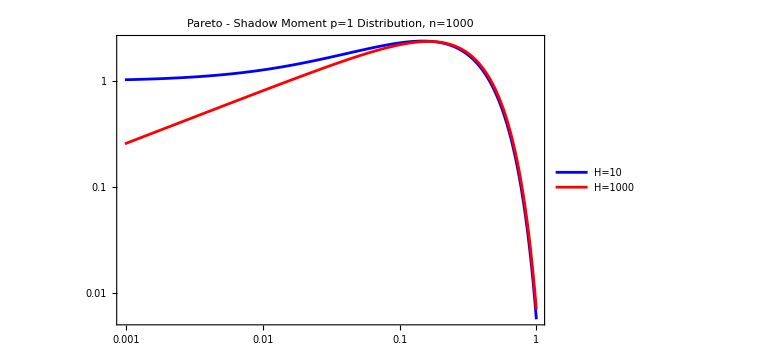

```mathematica
LogLogPlot[{
swtppdf[1,10,3,1,10,x],
swtppdf[1,1000,3,1,10,x]},
{x,0,1},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Distribution, n=1000",
PlotStyle->{Blue,Red},
PlotLegends->{"H=10","H=1000"}]
```

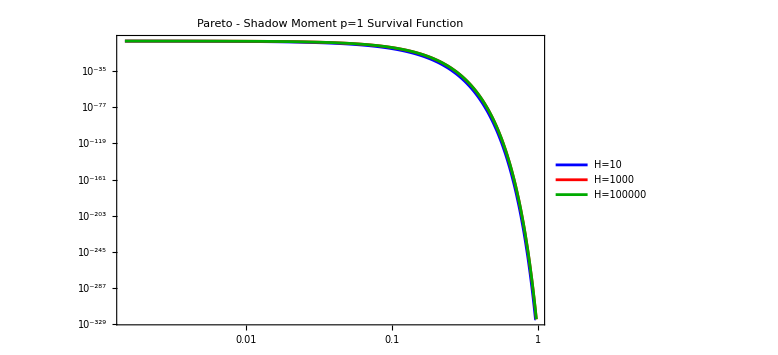

```mathematica
LogLogPlot[{
swtpSF[1,10,3,1,10^3,x],
swtpSF[1,1000,3,1,10^3,x],
swtpSF[1,100000,3,1,10^3,x]},
{x,0,3/2},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Survival Function",
PlotStyle->{Blue,Red,Darker[Green]},
PlotLegends->{"H=10","H=1000","H=100000"}]
```

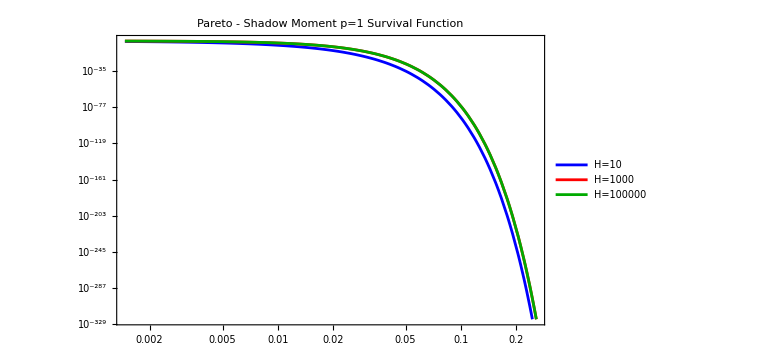

```mathematica
LogLogPlot[{
swtpSF[1,10,3,1,10^4,x],
swtpSF[1,1000,3,1,10^4,x],
swtpSF[1,100000,3,1,10^4,x]},
{x,0,3/2},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Survival Function",
PlotStyle->{Blue,Red,Darker[Green]},
PlotLegends->{"H=10","H=1000","H=100000"}]
```

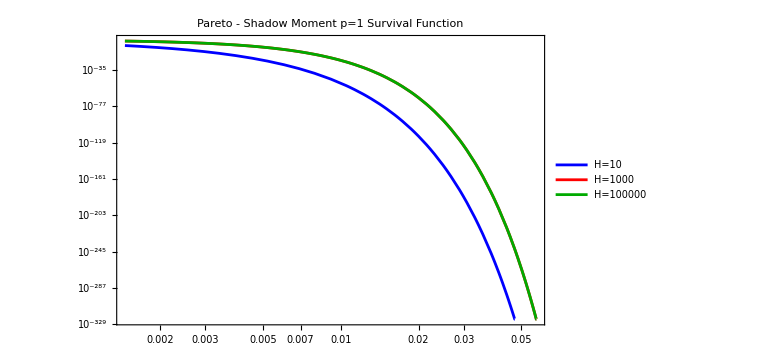

```mathematica
LogLogPlot[{
swtpSF[1,10,3,1,10^5,x],
swtpSF[1,1000,3,1,10^5,x],
swtpSF[1,100000,3,1,10^5,x]},
{x,0,3/2},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Survival Function",
PlotStyle->{Blue,Red,Darker[Green]},
PlotLegends->{"H=10","H=1000","H=100000"}]
```

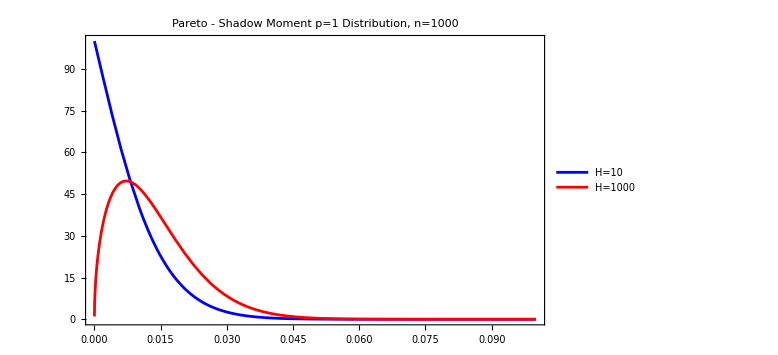

```mathematica
Plot[{
swtppdf[1,10,3,1,1000,x],
swtppdf[1,1000,3,1,1000,x]},
{x,0,0.1},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Distribution, n=1000",
PlotStyle->{Blue,Red},
PlotLegends->{"H=10","H=1000"}]
```

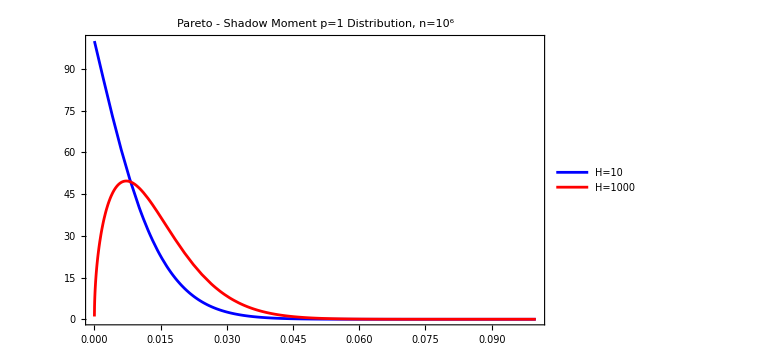

```mathematica
Plot[{
swtppdf[1,10,3,1,1000,x],
swtppdf[1,1000,3,1,1000,x]},
{x,0,0.1},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Distribution, n=10^6",
PlotStyle->{Blue,Red},
PlotLegends->{"H=10","H=1000"}]
```

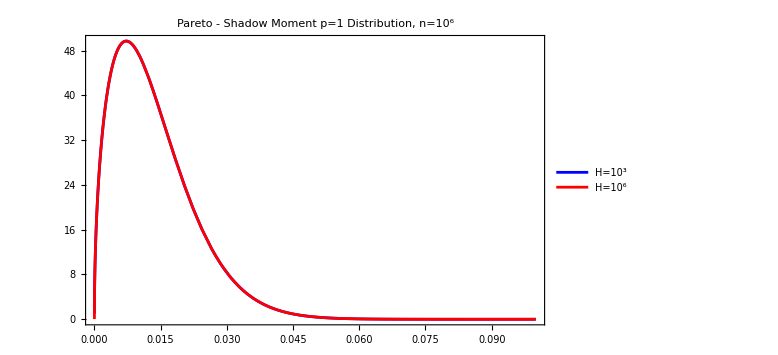

```mathematica
Plot[{
swtppdf[1,1000,3,1,1000,x],
swtppdf[1,1000000,3,1,1000,x]},
{x,0,0.1},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Distribution, n=10^6",
PlotStyle->{Blue,Red},
PlotLegends->{"H=10^3","H=10^6"}]
```

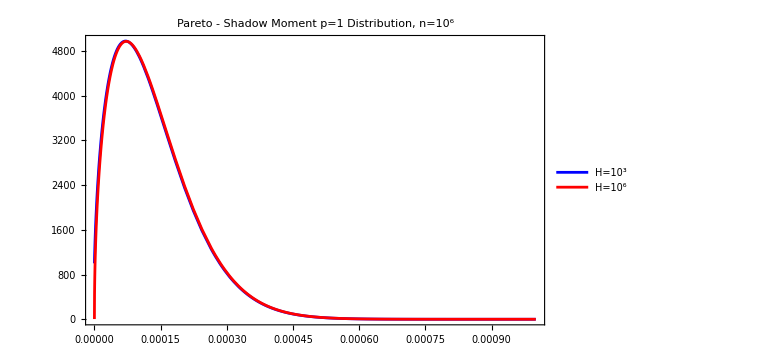

```mathematica
Plot[{
swtppdf[1,1000,3,1,1000000,x],
swtppdf[1,1000000,3,1,1000000,x]},
{x,0,0.001},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Distribution, n=10^6",
PlotStyle->{Blue,Red},
PlotLegends->{"H=10^3","H=10^6"}]
```

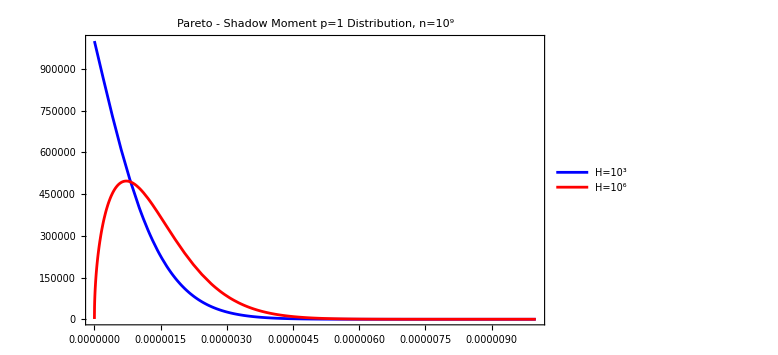

```mathematica
Plot[{
swtppdf[1,1000,3,1,1000000000,x],
swtppdf[1,1000000,3,1,1000000000,x]},
{x,0,0.00001},PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Pareto - Shadow Moment p=1 Distribution, n=10^9",
PlotStyle->{Blue,Red},
PlotLegends->{"H=10^3","H=10^6"}]
```

### Gaussian

```mathematica
Solve[Y==(1/2 Erfc[(-X+μ)/(√2 σ)])^n,X]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{X→μ-√2 σ InverseErfc[(2^n Y)^(1/n)]}}

```mathematica
μ==2^(p/2-1)/(√π)Gamma[(p+1)/2,(InverseErfc[2 y^(1/n)])^2]
```

```mathematica
FullSimplify[2^-1/(√π)Gamma[1/2,(InverseErfc[2 y^(1/n)])^2]]
```

1/2 Erfc[√(InverseErfc[2 y^(1/n)]^2)]

```mathematica
FullSimplify[2^(-1/2)/(√π)Gamma[1,(InverseErfc[2 y^(1/n)])^2]]
```

(ⅇ^(-InverseErfc[2 y^(1/n)]^2))/(√(2 π))

```mathematica
D[Erfc[√(-Log[√(2π)x])],x]
```

(√2)/(√(-Log[√(2 π) x]))

```mathematica
D[2^-n Erfc[-x/(√2)]^n,x]
```

(2^(1/2-n) ⅇ^(-x^2/2) n Erfc[-x/(√2)]^(-1+n))/(√π)

```mathematica
Integrate[(μ-√2 σ InverseErfc[2 p])(n*p^(n-1)),{p,0,1}]
```

∫_0^1 n p^(-1+n) (μ-√2 σ InverseErfc[2 p])ⅆp

```mathematica
Integrate[(μ-√2 σ InverseErfc[2 p])(n*p^(n-1)),{p,1/2,1}]
```

∫_(1/2)^1 n p^(-1+n) (μ-√2 σ InverseErfc[2 p])ⅆp

```mathematica
Table[{n,NIntegrate[(2^(1/2-n) ⅇ^(-x^2/2) n Erfc[-x/(√2)]^(-1+n))/(√π)x,{x,-∞,∞}]},{n,2,10}]
```

{{2,0.56419},{3,0.846284},{4,1.02938},{5,1.16296},{6,1.26721},{7,1.35218},{8,1.4236},{9,1.48501},{10,1.53875}}

```mathematica
Table[{n,NIntegrate[(0-√2 1 InverseErfc[2*p])(n*p^(n-1)),{p,0,1}]},{n,2,10}]
```

{{2,0.56419},{3,0.846284},{4,1.02938},{5,1.16296},{6,1.26721},{7,1.35218},{8,1.4236},{9,1.48501},{10,1.53875}}

```mathematica
Table[{n,NIntegrate[(2^(1/2-n) ⅇ^(-x^2/2) n Erfc[-x/(√2)]^(-1+n))/(√π)x,{x,0,∞}]},{n,2,10}]
```

{{2,0.681037},{3,0.888147},{4,1.04576},{5,1.1697},{6,1.27007},{7,1.35343},{8,1.42415},{9,1.48526},{10,1.53887}}

```mathematica
Table[{n,NIntegrate[(0-√2 1 InverseErfc[2*p])(n*p^(n-1)),{p,0.5,1}]},{n,2,10}]
```

{{2,0.681037},{3,0.888147},{4,1.04576},{5,1.1697},{6,1.27007},{7,1.35343},{8,1.42415},{9,1.48526},{10,1.53887}}

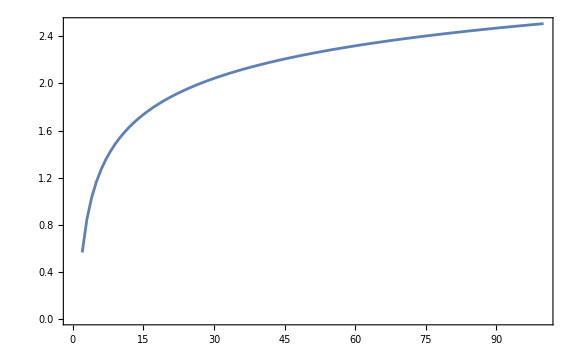

```mathematica
ListLinePlot[Table[{n,NIntegrate[(0-√2 1 InverseErfc[2*p])(n*p^(n-1)),{p,0,1}]},{n,2,100}],
Frame->True,PlotRange->All,ImageSize->Large,Filling->None]
```

```mathematica
gaussianKdist[n_,x_]:=(2^(1/2-n) ⅇ^(-x^2/2) n Erfc[-x/(√2)]^(-1+n))/(√π);
```

```mathematica
meangaussianf[n_]:=NIntegrate[(0-√2 1 InverseErfc[2*p])(n*p^(n-1)),{p,0,1}];
```

```mathematica
meangaussian3pts=Chop[N[Table[{n,meangaussianf[n],gaussianKdist[n,meangaussianf[n]]},
{n,10,1000,10}]]];
```

```mathematica
Show[DiscretePlot3D[gaussianKdist[n,x],{n,10,1000,10},{x,0,6,0.01},
PlotRange->All,ImageSize->Large,AxesLabel->Automatic,
ColorFunction->(ColorData["TemperatureMap"][#3]&),
PlotLabel->"Gaussian - Record Distribution and Mean",
Filling->None],
ListLinePlot3D[meangaussian3pts,PlotStyle->{Thick,Black}]]
```

-Graphics3D-

## Simulations

## Functions

```mathematica
histmax[sample_]:=Module[{samplemax,splmax,records,splrng,spldt},
samplemax=Rest[FoldList[Max,0,sample]];
splmax=Split[samplemax];
records=Map[First,splmax];
splrng=Range[Length[splmax]];
spldt=Map[Length,splmax];
samplemax];
```

```mathematica
shadowmeanmax[sample_]:=Module[{n,samplemax,splmax,records,spldt,locnewmax,shadow},
n=Length[sample];
samplemax=Rest[FoldList[Max,0,sample]];
splmax=Split[samplemax];
records=Map[First,splmax];
spldt=Map[Length,splmax];
locnewmax=Most[Accumulate[spldt]]+1;
shadow=Table[Total[Select[Drop[sample,locnewmax[[j]]],#>records[[j]]&]]/(n-locnewmax[[j]]),{j,1,Length[records]-1}];
Transpose[{locnewmax,Most[records],shadow}]];
```

```mathematica
shadowmeanln[pts_]:=Module[{n,rmax,splmax,maxpts,locnewmax,shadow},
n=Length[pts];
rmax=Rest[FoldList[Max,0,pts]];
splmax=Split[rmax];
maxpts=Map[First,splmax];
locnewmax=Most[Accumulate[Map[Length,splmax]]]+1;
shadow=Table[Total[Select[Drop[pts,locnewmax[[j]]],#>maxpts[[j]]&]]/(n-locnewmax[[j]]),{j,1,Length[maxpts]-1}];
Transpose[{locnewmax,Most[maxpts],shadow}]];
```

## Single path

```mathematica
SeedRandom[0];
unifdata=RandomVariate[UniformDistribution[{0,1}],10^4];
```

```mathematica
shmtest0=shadowmeanmax[unifdata]
```

{{3,0.652468,0.291524},{5,0.682813,0.270183},{6,0.935202,0.0615505},{82,0.976188,0.0213323},{375,0.987692,0.012289},{378,0.989229,0.0113671},{649,0.998288,0.0017093},{1665,0.998889,0.000839312},{7779,0.999779,0}}

```mathematica
test1=RandomVariate[UniformDistribution[{0,1}],100]
```

{0.460556,0.413643,0.0411558,0.497542,0.949944,0.723698,0.685772,0.115617,0.289159,0.27287,0.069664,0.467509,0.95953,0.113355,0.0745361,0.211968,0.256181,0.440134,0.747593,0.964644,0.668926,0.231446,0.0663833,0.852467,0.67823,0.85093,0.298949,0.718817,0.0457094,0.51336,0.497395,0.56209,0.681821,0.45752,0.346151,0.967957,0.763404,0.670901,0.114722,0.0163046,0.183882,0.860543,0.0544423,0.949377,0.429297,0.368374,0.0577547,0.569799,0.00364349,0.000820775,0.87613,0.186933,0.477916,0.61456,0.275611,0.786855,0.445393,0.617791,0.928344,0.300266,0.846017,0.118117,0.661172,0.934977,0.0663624,0.828588,0.367112,0.631388,0.122328,0.684918,0.0957869,0.852105,0.184906,0.142423,0.390869,0.167124,0.327623,0.229039,0.386633,0.907807,0.959116,0.25899,0.205697,0.565547,0.272101,0.406772,0.626759,0.510668,0.937495,0.222629,0.529774,0.647144,0.551899,0.0214512,0.79022,0.633372,0.843431,0.49665,0.792973,0.594806}

```mathematica
shmtest1=shadowmeanmax[test1]
```

{{4,0.460556,0.379512},{5,0.497542,0.353092},{13,0.949944,0.0332381},{20,0.95953,0.0120995},{36,0.964644,0}}

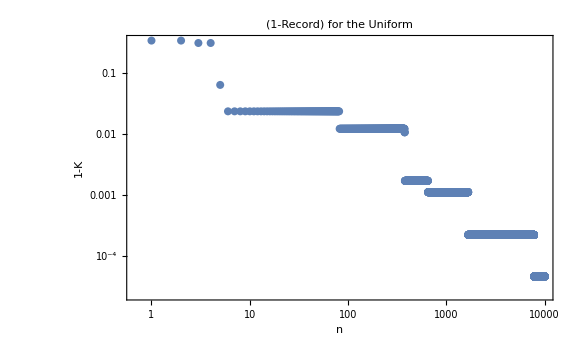

```mathematica
ListLogLogPlot[1-histmax[unifdata],
PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"(1-Record) for the Uniform",
PlotStyle->{PointSize[0.01]},
FrameLabel->{"n","1-K"}]
```

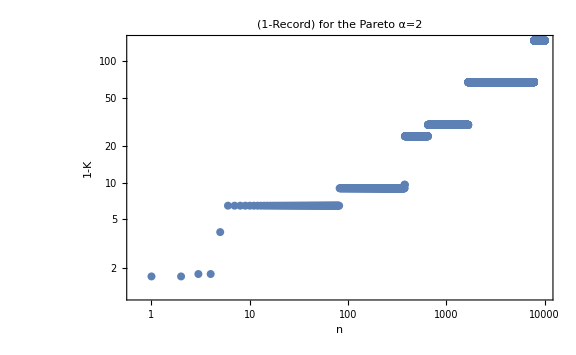

```mathematica
ListLogLogPlot[Map[(1*(1-#)^(-1/2))&,histmax[unifdata]],
PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"(1-Record) for the Pareto α=2",
PlotStyle->{PointSize[0.01]},
FrameLabel->{"n","1-K"}]
```

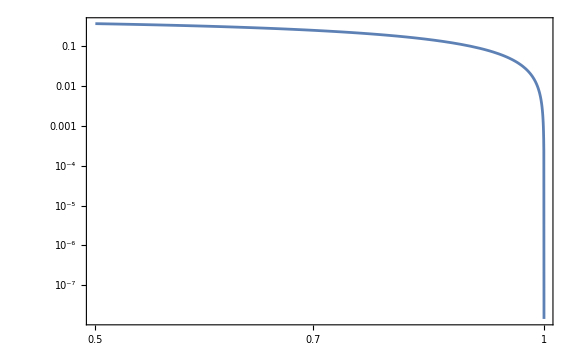

```mathematica
LogLogPlot[(1-K^2)/2,{K,0.5,1},PlotRange->All,ImageSize->Large,Frame->True]
```

```mathematica
Simplify[∑_(j=1)^∞ (j(1-K)K^(j-1))]
```

1/(1-K)

```mathematica
tblunifshm=Flatten[Table[{n,1/(1-K),n*K^(n-1)},{n,1,100},{K,0.001,0.999,0.001}],1];
```

```mathematica
ListPointPlot3D[tblunifshm,PlotRange->All,ImageSize->Large,AxesLabel->{"n","1/(1 - K)","n*K^(n - 1)"}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Map[{Log[#[[1]]],Log[#[[2]]],#[[3]]}&,tblunifshm],PlotRange->All,ImageSize->Large,
AxesLabel->{"Log[n]","Log[1/(1 - K)]","n*K^(n - 1)"}]
```

-Graphics3D-

```mathematica
Simplify[{1/(1-(n/(n+1))),(1-(n/(n+1))^2)/2}]
```

{1+n,(1+2 n)/(2 (1+n)^2)}

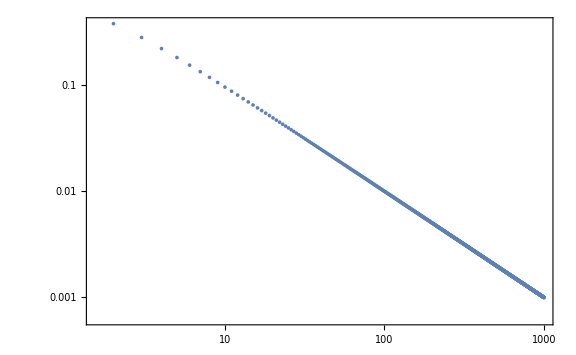

```mathematica
ListLogLogPlot[Table[{1/(1-(n/(n+1))),(1-(n/(n+1))^2)/2},{n,1,1000}],Frame->True,PlotRange->All,ImageSize->Large]
```

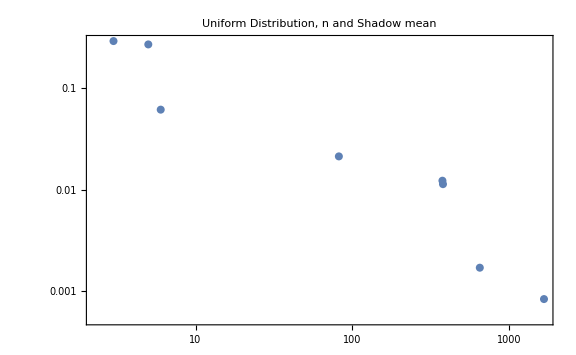

```mathematica
ListLogLogPlot[Map[{#[[1]],#[[3]]}&,shmtest0],
PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Uniform Distribution, n and Shadow mean",
PlotStyle->{PointSize[0.01]}]
```

## One path to rule them all

```mathematica
SeedRandom[0];
unifdata1=RandomVariate[UniformDistribution[{0,1}],10^7];
```

```mathematica
Timing[unifshmean1=shadowmeanmax[unifdata1];]
```

{58.2877,Null}

```mathematica
Take[unifdata1,10]
```

{0.652468,0.63307,0.682813,0.566352,0.935202,0.976188,0.238452,0.637562,0.101098,0.645525}

```mathematica
unifshmean1
```

{{3,0.652468,0.287322},{5,0.682813,0.267017},{6,0.935202,0.0626738},{82,0.976188,0.0235539},{375,0.987692,0.0122513},{378,0.989229,0.0107297},{649,0.998288,0.00170764},{1665,0.998889,0.00110067},{7779,0.999779,0.000217445},{14276,0.999954,0.0000427601},{224524,0.999978,0.0000209706},{249458,0.999998,1.43582×10^-6},{4622431,1.,1.85958×10^-7}}

```mathematica
shadowmeantrio[sample_]:=Module[{n,samplemax,splmax,records,spldt,locnewmax,shadow},
n=Length[sample];
samplemax=Rest[FoldList[Max,0,sample]];
splmax=Split[samplemax];
records=Map[First,splmax];
spldt=Map[Length,splmax];
locnewmax=Prepend[Most[Accumulate[spldt]]+1,1];
shadow=Table[
Total[Select[Drop[sample,locnewmax[[j]]],#>records[[j]]&]]/(n-locnewmax[[j]]),
{j,1,Length[records]}];
Transpose[{locnewmax,records,shadow}]];
```

```mathematica
Timing[unifshmean1new=shadowmeantrio[unifdata1];]
```

{62.8593,Null}

```mathematica
unifshmean1new
```

{{1,0.652468,0.287322},{3,0.682813,0.267017},{5,0.935202,0.0626739},{6,0.976188,0.0235538},{82,0.987692,0.012251},{375,0.989229,0.0107298},{378,0.998288,0.0017077},{649,0.998889,0.00110066},{1665,0.999779,0.000217412},{7779,0.999954,0.0000428323},{14276,0.999978,0.0000206292},{224524,0.999998,1.53445×10^-6},{249458,1.,2.05117×10^-7},{4622431,1.,0}}

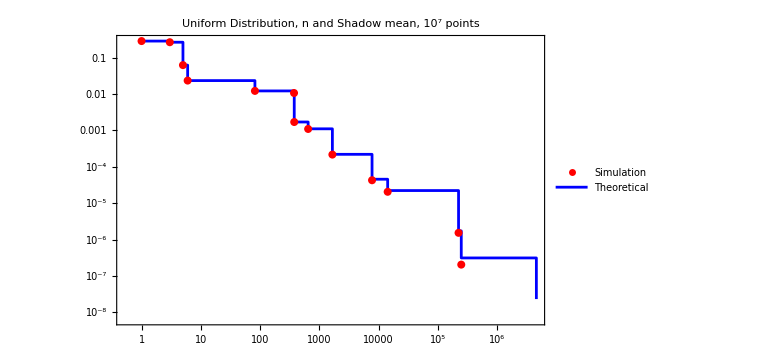

```mathematica
ListLogLogPlot[{Map[{#[[1]],#[[3]]}&,unifshmean1new],Map[{#[[1]],(1-(#[[2]])^2)/2}&,unifshmean1new]},
PlotRange->All,ImageSize->Large,Frame->True,
PlotLabel->"Uniform Distribution, n and Shadow mean, 10^7 points",
PlotStyle->{{Red,PointSize[0.01]},{Blue,PointSize[0.01]}},
PlotLegends->{"Simulation","Theoretical"},Joined->{False,True},
InterpolationOrder->0]
```

## Lots of paths

```mathematica
SeedRandom[45];
unifdata1k=Table[RandomVariate[UniformDistribution[{0,1}],10^5],1000];
```

```mathematica
Timing[unifshmean1k=Map[shadowmeanmax,unifdata1k];]
```

$Aborted

```mathematica
Timing[gaussiandata1k=Map[(0-√2 1 InverseErfc[2 #])&,unifdata1k,{2}];]
```

{1244.11,Null}

```mathematica
Timing[gaussianshmean1k=Map[shadowmeanmax,gaussiandata1k];]
```

{439.957,Null}

```mathematica
Timing[paretodata1k=Map[(1 (1-#)^(-1/2))&,unifdata1k,{2}];]
```

{85.4279,Null}

```mathematica
Timing[paretoshmean1k=Map[shadowmeanmax,paretodata1k];]
```

{449.536,Null}

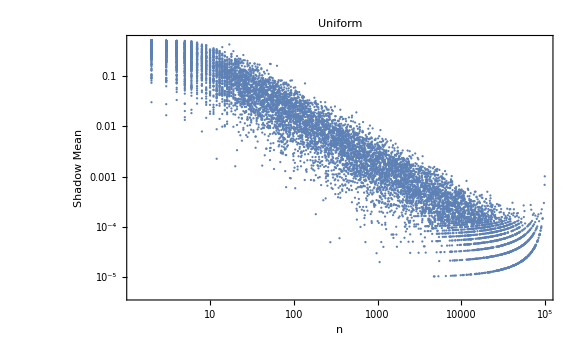

```mathematica
ListLogLogPlot[Map[{#[[1]],#[[3]]}&,Flatten[unifshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"n","Shadow Mean"},PlotLabel->"Uniform"]
```

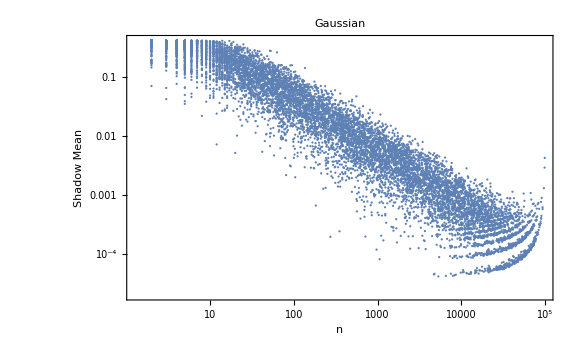

```mathematica
ListLogLogPlot[Map[{#[[1]],#[[3]]}&,Flatten[gaussianshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"n","Shadow Mean"},PlotLabel->"Gaussian"]
```

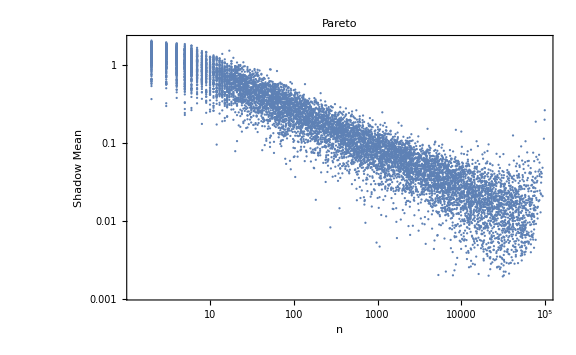

```mathematica
ListLogLogPlot[Map[{#[[1]],#[[3]]}&,Flatten[paretoshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"n","Shadow Mean"},PlotLabel->"Pareto"]
```

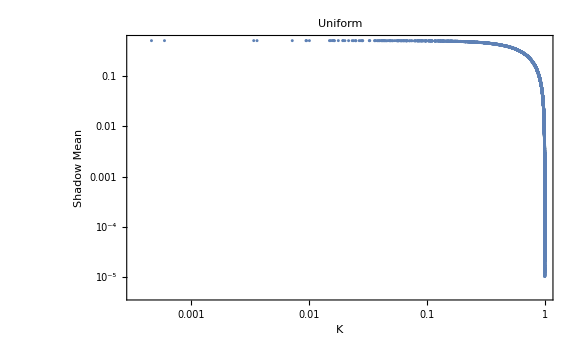

```mathematica
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Flatten[unifshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"K","Shadow Mean"},PlotLabel->"Uniform"]
```

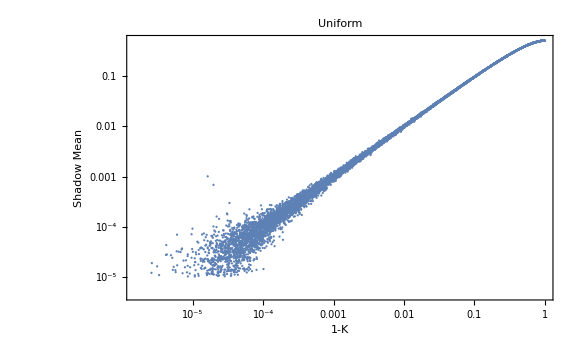

```mathematica
ListLogLogPlot[Map[{1-#[[2]],#[[3]]}&,Flatten[unifshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"1-K","Shadow Mean"},PlotLabel->"Uniform"]
```

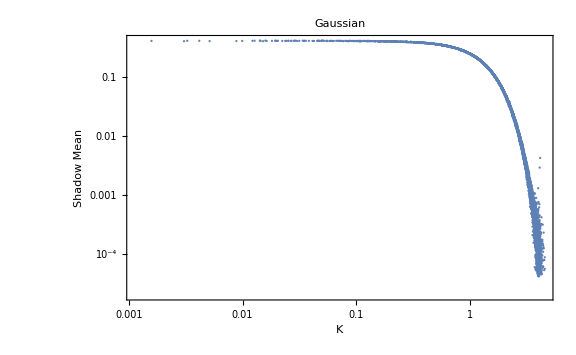

```mathematica
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Flatten[gaussianshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"K","Shadow Mean"},PlotLabel->"Gaussian"]
```

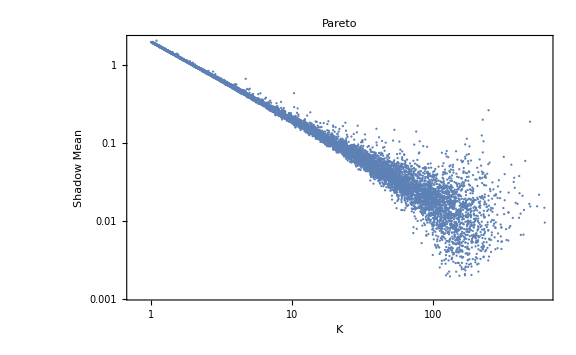

```mathematica
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Flatten[paretoshmean1k,1]],
PlotRange->All,ImageSize->Large,Frame->True,
FrameLabel->{"K","Shadow Mean"},PlotLabel->"Pareto"]
```

```mathematica
Histogram3D[Map[Log[{#[[1]],#[[3]]}]&,Flatten[unifshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[n]","Log[Shadow Mean]"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Uniform"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[Log[{#[[1]],#[[3]]}]&,Flatten[gaussianshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[n]","Log[Shadow Mean]"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Gaussian"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[{Log[#[[1]]],#[[3]]}&,Flatten[paretoshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[n]","Shadow Mean"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Pareto"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[Log[{#[[1]],#[[3]]}]&,Flatten[paretoshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[n]","Log[Shadow Mean]"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Pareto"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[Log[{1-#[[2]],#[[3]]}]&,Flatten[unifshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[1-K]","Log[Shadow Mean]"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Uniform"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[{#[[2]],#[[3]]}&,Flatten[gaussianshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"K","Shadow Mean"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Gaussian"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[Log[{#[[2]],#[[3]]}]&,Flatten[gaussianshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[K]","Log[Shadow Mean]"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Gaussian"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[{#[[2]],#[[3]]}&,Flatten[paretoshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"K","Shadow Mean"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Pareto"]
```

-Graphics3D-

```mathematica
Histogram3D[Map[Log[{#[[2]],#[[3]]}]&,Flatten[paretoshmean1k,1]],
PlotRange->All,ImageSize->Large,AxesLabel->{"Log[K]","Log[Shadow Mean]"},
ChartElementFunction->"GradientScaleCube",PlotLabel->"Pareto"]
```

-Graphics3D-